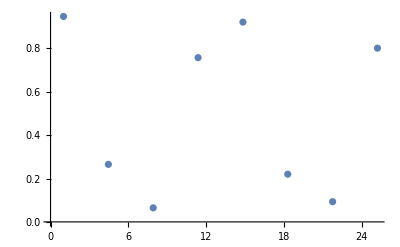

```mathematica
x=Subdivide[1,4*6.3,8-1];
y=Cos[π/(2 6.8)# ]^2&/@x;
ListPlot[Transpose@{x,y}]
```

Units

```mathematica
um=Quantity[1,"Micrometers"];
debye=Quantity[1,"Debyes"];
```

Fundamental constants

```mathematica
ϵ0=Quantity["Permittivity of free space"];
ℏ=Quantity["ReducedPlanckConstant"];
h=Quantity["PlanckConstant"];
```

Parameters

```mathematica
θ=π/2; (*the array is orthogonal to the B-field direction*)
r=1.5 um;
d=4.6/(√3) debye;
Jperp=2(d)^2/(4π ϵ0);
δω0={0,0};qubits=2;
```

```mathematica
d//UnitConvert
```

8.85883×10^-30 m s A

```mathematica
d//UnitConvert
```

8.85883×10^-30 m s A

Operators

```mathematica
σ={σx,σy,σz}=(PauliMatrix[#1]&)/@{1,2,3};σp=σx+ⅈ σy;σm=σx-ⅈ σy;
{Sp,Sm}={σp,σm}/2;
```

Hermitian conjugate

```mathematica
conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj;
```

State

```mathematica
g=({{1}, {0}});e=({{0}, {1}});gg=KroneckerProduct[g,g];
```

Hamiltonian

```mathematica
HDD=(1-3 Cos[θ]^2)/(ℏ r^3)Jperp/2(KroneckerProduct[Sp,Sm]+hc[KroneckerProduct[Sp,Sm]]);
```

```mathematica
HDD=UnitConvert[HDD,1/("Seconds")]//QuantityMagnitude(*divide by 2π for Hz*)
```

{{0.,0.,0.,0.},{0.,0.,1981.73,0.},{0.,1981.73,0.,0.},{0.,0.,0.,0.}}

```mathematica
HJ=HDD/.Max[HDD]->J;
Hpulse[vec_]:=1/2 Ω ∑_(n=1)^3 σ⟦n⟧ Normalize[vec]⟦n⟧
H0Single[n_]:=1/2 δω0⟦n⟧ σz
Hphase=({{-ΔE, 0}, {0, ΔE}});
Hphase=KroneckerProduct[Hphase,IdentityMatrix[2]];
H0=KroneckerProduct[IdentityMatrix[2],H0Single[2]]+KroneckerProduct[H0Single[1],IdentityMatrix[2]]+HJ;idList=ConstantArray[IdentityMatrix[2],qubits];
H[vec_,numbers_]:=H0+Plus@@Table[KroneckerProduct@@ReplacePart[idList,i->Hpulse[vec]],{i,numbers}];
```

Matrices for the dipolar interaction and for a global, single particle π/2pulse, and a single particle phase gate

```mathematica
(mDD=MatrixExp[-ⅈ t1(H[{-1,0,0},{1,2}]/.Ω->0)]//FullSimplify)//MatrixForm
(mP2p1=MatrixExp[-ⅈ π/(2Ω)(H[{-1,0,0},{1}]/.J->0)]//FullSimplify)//MatrixForm
(mP2p2=MatrixExp[-ⅈ π/(2Ω)(H[{-1,0,0},{2}]/.J->0)]//FullSimplify)//MatrixForm
(mP2p12=MatrixExp[-ⅈ π/(2Ω)(H[{-1,0,0},{1,2}]/.J->0)]//FullSimplify)//MatrixForm
(mPhase=MatrixExp[-ⅈ t2 Hphase]//FullSimplify)//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[J t1] | -ⅈ Sin[J t1] | 0
0 | -ⅈ Sin[J t1] | Cos[J t1] | 0
0 | 0 | 0 | 1)

(1/(√2) | 0 | ⅈ/(√2) | 0
0 | 1/(√2) | 0 | ⅈ/(√2)
ⅈ/(√2) | 0 | 1/(√2) | 0
0 | ⅈ/(√2) | 0 | 1/(√2))

(1/(√2) | ⅈ/(√2) | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | ⅈ/(√2)
0 | 0 | ⅈ/(√2) | 1/(√2))

(1/2 | ⅈ/2 | ⅈ/2 | -1/2
ⅈ/2 | 1/2 | -1/2 | ⅈ/2
ⅈ/2 | -1/2 | 1/2 | ⅈ/2
-1/2 | ⅈ/2 | ⅈ/2 | 1/2)

(ⅇ^(ⅈ t2 ΔE) | 0 | 0 | 0
0 | ⅇ^(ⅈ t2 ΔE) | 0 | 0
0 | 0 | ⅇ^(-ⅈ t2 ΔE) | 0
0 | 0 | 0 | ⅇ^(-ⅈ t2 ΔE))

The operation below corresponds to (1) starting in gg, (2) applying a global single particle pi/2 pulse, (3) dipole-dipole interaction for t= π/(2J), (3) another global single particle pi/2 pulse,

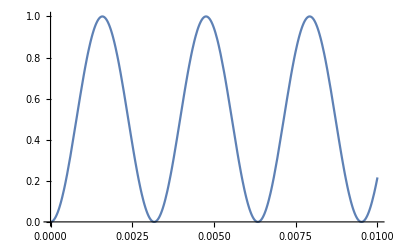

```mathematica
Plot[Abs[ggᵀ.mP2p12.mDD.mP2p12.gg]^2/.J->Max[HDD],{t1,0,10 10^-3}]
```

```mathematica
Max[HDD]/(2π)
```

315.402

The interaction time is 792 us.

```mathematica
10^6 π/J/.J->Max[HDD]
```

1585.28

```mathematica
mDD.gg
```

{{1},{0},{0},{0}}

```mathematica
mDD//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[J t1] | -ⅈ Sin[J t1] | 0
0 | -ⅈ Sin[J t1] | Cos[J t1] | 0
0 | 0 | 0 | 1)

```mathematica
1/((2π)/J)
```

J/(2 π)

```mathematica
Max[HDD]
```

1981.73